```mathematica
link=Install[LinkConnect["34269@192.168.150.130,40517@192.168.150.130",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle =With[
{c=5,Ωp=1/1836,Ωe=-1,ωbeame=5*Sqrt[0.05],ωbacke=5*Sqrt[0.95],ωp=5/Sqrt[1836],θbeamepara=Sqrt[5]*0.1,θbeameperp=5*Sqrt[5]*0.1,θbackepara=Sqrt[50]*0.001,θbackeperp=Sqrt[50]*0.001,θp=Sqrt[50/1836]*0.001,vdbeame=1,vdbacke=-1/19,vdp=0

},
dist=
Thread[wstpDRingDistribution[{Ωe,Ωe,Ωp},{ωbeame,ωbacke,ωp},{θbeamepara,θbackepara,θp},{θbeameperp,θbackeperp,θp},{vdbeame,vdbacke,vdp}]]
;
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
r=Complex[4.1,0.65];
test=wstpDFindRoot[handle,5.7,0.0,r (1+0.0001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
test;
solution=test[[2,2]];
omega=Re[solution];
Dmatrix=test[[5,2]];
calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,(*分支1：平行传播，D13≈0，直接用D11、D12计算*)-Dmat[[1,1]]/Dmat[[1,2]],(*分支2：通用情况，余子式法*)
-(Dmat[[2,1]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,1]])/(Dmat[[2,2]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,2]])
]];

EyoverEx=calcEyOverEx[Dmatrix];
Re[EyoverEx/I*omega/Abs[omega]];
P=2/Pi*Arg[EyoverEx]*omega/Abs[omega];
```

0.822152

{{90}}

4.12328+0.822152 i

5.45

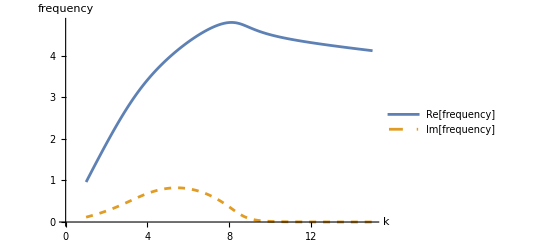

```mathematica
r=Complex[4.1,0.65];
dk=0.05;
kparaMin=1;   (*k平行下限*)
kmid=5.7;      (*收敛良好的中间起点*)
kparaMax=15;    (*k平行上限*)
kperpVal=0.0;    (*垂直波矢固定标量值*)

(*公共求解参数，只写一次*)
initGuess=r (1+0.0001 I {0,1,2});
solveOpts={"ReturnDispersionMatrix"->True,MaxIterations->100};

(*1. 向左段：kmid 往 kparaMin 递减遍历平行波矢*)
kparaLeft=Range[kmid,kparaMin,-dk];
(*把标量垂直分量扩充为和kparaLeft等长数组*)
kperpLeft=ConstantArray[kperpVal,Length[kparaLeft]];
solutionLeft=wstpDFindRoot[handle,kparaLeft,kperpLeft,initGuess,solveOpts];

(*2. 向右段：kmid+dk 往 kparaMax 递增，避免中点重复计算*)
kparaRight=Range[kmid+dk,kparaMax,dk];
kperpRight=ConstantArray[kperpVal,Length[kparaRight]];
solutionRight=wstpDFindRoot[handle,kparaRight,kperpRight,initGuess,solveOpts];

(*左段k从大到小，反转频率匹配升序k平行；拼接完整频率*)
freqLeftRev=Reverse[solutionLeft[[2,2]]];
frequency=Join[freqLeftRev,solutionRight[[2,2]]];
matrixLeftRev=Reverse[solutionLeft[[5,2]]];
matrix=Join[matrixLeftRev,solutionRight[[5,2]]];
k=Range[kparaMin,kparaMax,dk];
omega=Re[frequency];
gamma=Im[frequency];
calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,
-Dmat[[1,1]]/Dmat[[1,2]],-Det[Dmat[[{1,2},{1,3}]]]/Det[Dmat[[{1,2},{2,3}]]]]];

EyoverEx=calcEyOverEx/@matrix;


P=2/Pi*Arg[EyoverEx]*omega/Abs[omega];

Max[Im[frequency]]
Position[Im[frequency],Max[Im[frequency]]]
p=Position[Im[frequency],Max[Im[frequency]]][[1,1]];
Re[frequency][[p]]+i Im[frequency][[p]]
kparaMin+dk*(p-1)
ListLinePlot[{Transpose[{k,Re[frequency]}],Transpose[{k,Im[frequency]}]},PlotStyle->{Solid,Dashed},PlotLegends->{"Re[frequency]","Im[frequency]"},AxesLabel->{"k","frequency"}]
```

```mathematica
r=Complex[-0.026,0.01];
dkpara=0.0005;
kparamin=0.01;
kparamid=0.03;
kparamax=0.5;
dkperp=0.05;
kperpmin=0.0;
kperpmid=0.0;
kperpmax=0.5;

(*两段垂直波矢网格*)
kp1=Range[kperpmid,kperpmax,dkperp];
kp2=Range[kperpmid,kperpmin,-dkperp];
allKperp=Union[kp1,kp2];

(*批量求解所有kperp在kparamid处的基准解（仅用于构造初值，不需要存D矩阵）*)
baseKparaVecdown=kparamid*ConstantArray[1,Length[kp2]];
baseKparaVecup=kparamid*ConstantArray[1,Length[kp1]];

baseSoldown=wstpDFindRoot[handle,baseKparaVecdown,kp2,r (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
baseSolup=wstpDFindRoot[handle,baseKparaVecup,kp1,r (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];

baseSolAll=Join[Reverse[baseSoldown[[2,2]]],Rest[baseSolup[[2,2]]]];
DofbaseSolAll=Join[Reverse[baseSoldown[[5,2]]],Rest[baseSolup[[5,2]]]];

(*建立{kperp,基准根}查表库，用于给每行提供初值*)
baseGuessTable=Transpose[{allKperp,baseSolAll}];
GetBaseGuess[kp_]:=Module[{match},match=Cases[baseGuessTable,{kp,val_}->val];
If[match=={},r,First[match]]]
```

```mathematica
allKperp;
baseSolAll;
DofbaseSolAll;
omega=Re[baseSolAll];
calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,
-Dmat[[1,1]]/Dmat[[1,2]],-Det[Dmat[[{1,2},{1,3}]]]/Det[Dmat[[{1,2},{2,3}]]]]];

EyoverEx=calcEyOverEx/@DofbaseSolAll;

P=2/Pi*Arg[EyoverEx]*omega/Abs[omega]
```

{1.,0.629779,0.973114,0.973681,0.961426}

```mathematica
(* ==========a4：kperp上半段，kpara向左递减==========*)a4=With[{kperpList=Rest[kp1]},Table[With[{kpara=Range[kparamid,kparamin,-dkpara]},currentInit=GetBaseGuess[kperp];
sol=wstpDFindRoot[handle,kpara,ConstantArray[kperp,Length[kpara]],currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
(*同时输出：频率向量、对应D矩阵向量*){sol[[2,2]],sol[[5,2]]}],{kperp,kperpList}]];

(* ==========a1：kperp上半段，kpara向右递增==========*)
a1=With[{kperpList=Rest[kp1]},Table[With[{kpara=Range[kparamid+dkpara,kparamax,dkpara]},currentInit=GetBaseGuess[kperp];
sol=wstpDFindRoot[handle,kpara,ConstantArray[kperp,Length[kpara]],currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}],{kperp,kperpList}]];

(* ==========a2：kperp下半段，kpara向右递增==========*)
a2=With[{kperpList=kp2},Table[With[{kpara=Range[kparamid+dkpara,kparamax,dkpara]},currentInit=GetBaseGuess[kperp];
sol=wstpDFindRoot[handle,kpara,ConstantArray[kperp,Length[kpara]],currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}],{kperp,kperpList}]];

(* ==========a3：kperp下半段，kpara向左递减==========*)
a3=With[{kperpList=kp2},Table[With[{kpara=Range[kparamid,kparamin,-dkpara]},currentInit=GetBaseGuess[kperp];
sol=wstpDFindRoot[handle,kpara,ConstantArray[kperp,Length[kpara]],currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}],{kperp,kperpList}]];
(*辅助函数：从每部分结果中提取频率数组/D矩阵数组*)extractFreq[part_]:=part[[All,1]];
extractMat[part_]:=part[[All,2]];

(*---上半段：a4反转后与a1拼接，kpara从左到右=min->max---*)
freq4Rev=Map[Reverse,extractFreq[a4]];
mat4Rev=Map[Reverse,extractMat[a4]];
freqRight=Join[freq4Rev,extractFreq[a1],2];
matRight=Join[mat4Rev,extractMat[a1],2];

(*---下半段：a3反转后与a2拼接---*)
freq3Rev=Map[Reverse,extractFreq[a3]];
mat3Rev=Map[Reverse,extractMat[a3]];
freqLeft=Join[freq3Rev,extractFreq[a2],2];
matLeft=Join[mat3Rev,extractMat[a2],2];

(*---上下半段拼接成完整二维网格---*)
(*行：kperp从小到大；列：kpara从小到大*)
freqTotal=Join[Reverse[freqLeft],freqRight];
matTotal=Join[Reverse[matLeft],matRight];

(*对应坐标数组，方便绘图和索引*)
kparaGrid=Range[kparamin,kparamax,dkpara];
kperpGrid=Sort[allKperp];
(*偏振比计算函数：和你单点、单线的逻辑完全一致*)calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,(*平行传播：D13≈0，直接用第一行系数计算*)-Dmat[[1,1]]/Dmat[[1,2]],(*斜传播：前两行消元法，对应你推导的展开式*)-(Dmat[[2,1]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,1]])/(Dmat[[2,2]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,2]])]];

(*二维批量计算Ey/Ex：对每个D矩阵应用函数，得到同维度二维数组*)
EyOverExTotal=Map[calcEyOverEx,matTotal,{2}];

(*元素级计算极化率P，和你单线公式完全一致：P=(2/π)·arg(Ey/Ex)·Re(ω)/|Re(ω)|*)
omegaReal=Re[freqTotal];

ReP=Re[EyOverExTotal/I*omegaReal/Abs[omegaReal]];
Max[Im[freqTotal]]
Position[Im[freqTotal],Max[Im[freqTotal]]]
freqTotal[[Position[Im[freqTotal],Max[Im[freqTotal]]][[1,1]],Position[Im[freqTotal],Max[Im[freqTotal]]][[1,2]]]]
kparamin+dkpara*(Position[Im[freqTotal],Max[Im[freqTotal]]][[1,2]]-1)
kperpmin+dkperp*(Position[Im[freqTotal],Max[Im[freqTotal]]][[1,1]]-1)
```

0.0100531

{{1,39}}

-0.0265742+0.0100531 ⅈ

0.029

0.

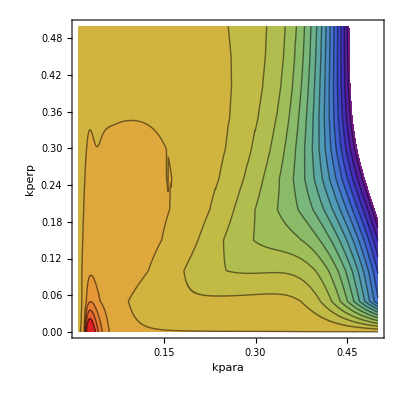

-Graphics-

```mathematica
ListContourPlot[Im[freqTotal],DataRange->{{kparamin,kparamax},{kperpmin,kperpmax}},(*关键选项*)AxesLabel->{"kpara","kperp"},Frame->True,ColorFunction->"Rainbow",Contours->20]

(*极化率P的等高线图*)
ListContourPlot[ReP,DataRange->{{kparamin,kparamax},{kperpmin,kperpmax}},(*关键选项*)AxesLabel->{"kpara","kperp"},Frame->True,ColorFunction->"Rainbow",Contours->20]
```

```mathematica
ListContourPlot[2/Pi*Arg[EyOverExTotal]*omegaReal/Abs[omegaReal],DataRange->{{kparamin,kparamax},{kperpmin,kperpmax}},(*关键选项*)AxesLabel->{"kpara","kperp"},Frame->True,ColorFunction->"Rainbow",Contours->20]
```

```mathematica
Max[ReP]
Max[2/Pi*Arg[EyOverExTotal]*omegaReal/Abs[omegaReal]]
Min[ReP]
Position[ReP,Max[ReP]]
kparamin+dkpara*(Position[ReP,Max[ReP]][[1,2]]-1)
kperpmin+dkperp*(Position[ReP,Max[ReP]][[1,1]]-1)
freqTotal[[Position[ReP,Max[ReP]][[1,1]],Position[ReP,Max[ReP]][[1,2]]]]
```

1.49348

1.22195

-0.997141

{{4,46}}

0.055

0.015

-0.062436+0.00170888 ⅈ

```mathematica
Export["case1_right2d_gamma_0.01:0.001:0.5_0:0.005:0.2.csv",Im[freqTotal]];
Export["case1_right2d_ReP_0.01:0.001:0.5_0:0.005:0.2.csv",ReP];
```

```mathematica
r=Complex[-0.062,0.0017];
test=wstpDFindRoot[handle,0.055,0.015,r (1+0.0001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
test
solution=test[[2,2]];
omega=Re[solution];
Dmatrix=test[[5,2]]
calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,(*分支1：平行传播，D13≈0，直接用D11、D12计算*)-Dmat[[1,1]]/Dmat[[1,2]],(*分支2：通用情况，余子式法*)
-(Dmat[[2,1]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,1]])/(Dmat[[2,2]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,2]])
]];

EyoverEx=calcEyOverEx[Dmatrix]
Re[EyoverEx/I*omega/Abs[omega]]
P=2/Pi*Arg[EyoverEx]*omega/Abs[omega]
```

{flag→0,ω→-0.062436+0.00170888 ⅈ,k1→0.055,k2→0.015,D→{{1.10516×10^7-530973. ⅈ,-2.30937×10^6-6.76606×10^6 ⅈ,1.45669×10^7+102074. ⅈ},{2.30937×10^6+6.76606×10^6 ⅈ,5.13278×10^6-1.52434×10^6 ⅈ,-5.30809×10^7+3.47405×10^8 ⅈ},{1.45669×10^7+102074. ⅈ,5.30809×10^7-3.47405×10^8 ⅈ,6.26191×10^10-2.419×10^10 ⅈ}}}

{{1.10516×10^7-530973. ⅈ,-2.30937×10^6-6.76606×10^6 ⅈ,1.45669×10^7+102074. ⅈ},{2.30937×10^6+6.76606×10^6 ⅈ,5.13278×10^6-1.52434×10^6 ⅈ,-5.30809×10^7+3.47405×10^8 ⅈ},{1.45669×10^7+102074. ⅈ,5.30809×10^7-3.47405×10^8 ⅈ,6.26191×10^10-2.419×10^10 ⅈ}}

0.443894-1.49348 ⅈ

1.49348

0.816077

```mathematica
Dmatrix
```

{{1.10516×10^7-530973. ⅈ,-2.30937×10^6-6.76606×10^6 ⅈ,1.45669×10^7+102074. ⅈ},{2.30937×10^6+6.76606×10^6 ⅈ,5.13278×10^6-1.52434×10^6 ⅈ,-5.30809×10^7+3.47405×10^8 ⅈ},{1.45669×10^7+102074. ⅈ,5.30809×10^7-3.47405×10^8 ⅈ,6.26191×10^10-2.419×10^10 ⅈ}}

```mathematica
EyoverEx=calcEyOverEx[Dmatrix]
```

0.443894-1.49348 ⅈ

```mathematica
Re[EyoverEx/I*omega/Abs[omega]]
```

1.49348

```mathematica
2/Pi*Arg[EyoverEx]*omega/Abs[omega]
```

0.816077

```mathematica
r=Complex[-0.026,0.01];
dkpara=0.002;
kparamin=0.01;
kparamid=0.03;
kparamax=0.5;
dkperp=0.01;
kperpmin=0.0;
kperpmid=0.0;
kperpmax=0.5;

(*kperp两段网格（沿用原定义，上下扫描用）*)kp1=Range[kperpmid,kperpmax,dkperp];  (*上半段：mid->max*)
kp2=Range[kperpmid,kperpmin,-dkperp]; (*下半段：mid->min*)
allKperp=Union[kp1,kp2];


(*kpara两段网格（对应原kp1/kp2的角色，基准线用）*)
kparaRight=Range[kparamid,kparamax,dkpara];  (*右半段：mid->max*)
kparaLeft=Range[kparamid,kparamin,-dkpara];  (*左半段：mid->min*)
allKpara=Union[kparaRight,kparaLeft];

(* =====================1. 基准解：固定kperp=mid，扫全kpara=====================*)
(*基准线：kperp固定为中间值，扫描kpara左右两段，建立初值查表库*)
baseKperpVal=kperpmid;

baseSolLeft=wstpDFindRoot[handle,kparaLeft,ConstantArray[baseKperpVal,Length[kparaLeft]],r (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];

baseSolRight=wstpDFindRoot[handle,Rest[kparaRight],ConstantArray[baseKperpVal,Length[Rest[kparaRight]]],r (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];

(*拼接基准解：kpara从小到大排列*)
baseSolAll=Join[Reverse[baseSolLeft[[2,2]]],baseSolRight[[2,2]]];
DofbaseSolAll=Join[Reverse[baseSolLeft[[5,2]]],baseSolRight[[5,2]]];
(*建立{kpara->基准根}查表函数，给每列扫描提供起点初值*)baseGuessTable=Transpose[{Sort[allKpara],baseSolAll}];
GetBaseGuessKpara[kpara_]:=Module[{match},match=Cases[baseGuessTable,{kpara,val_}->val];
If[match=={},r,First[match]]]
```

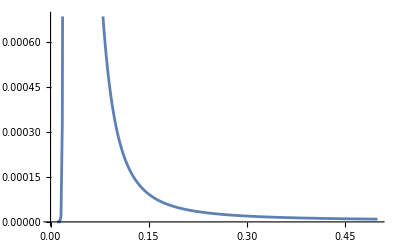

```mathematica
allKpara;
baseSolAll;
DofbaseSolAll;
omega=Re[baseSolAll];
gamma=Im[baseSolAll];
calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,
-Dmat[[1,1]]/Dmat[[1,2]],-Det[Dmat[[{1,2},{1,3}]]]/Det[Dmat[[{1,2},{2,3}]]]]];
EyoverEx=calcEyOverEx/@DofbaseSolAll;
ListLinePlot[Transpose[{allKpara,gamma}]]
P=Re[EyoverEx/I*omega/Abs[omega]];
```

```mathematica
b1=With[{kparaList=Rest[kparaRight]},Table[With[{kperp=kp1},currentInit=GetBaseGuessKpara[kpara];
sol=wstpDFindRoot[handle,ConstantArray[kpara,Length[kperp]],(*固定当前kpara*)kperp,(*遍历kperp*)currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}  (*{频率向量,D矩阵向量}，对应kp1顺序*)],{kpara,kparaList}]];

(*----------b2：kpara右半段，kperp向下（mid->min）----------*)
b2=With[{kparaList=Rest[kparaRight]},Table[With[{kperp=kp2},currentInit=GetBaseGuessKpara[kpara];
sol=wstpDFindRoot[handle,ConstantArray[kpara,Length[kperp]],kperp,currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}  (*对应kp2顺序：mid->min*)],{kpara,kparaList}]];

(*----------b3：kpara左半段，kperp向下（mid->min）----------*)
b3=With[{kparaList=kparaLeft},Table[With[{kperp=kp2},currentInit=GetBaseGuessKpara[kpara];
sol=wstpDFindRoot[handle,ConstantArray[kpara,Length[kperp]],kperp,currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}],{kpara,kparaList}]];

(*----------b4：kpara左半段，kperp向上（mid->max）----------*)
b4=With[{kparaList=kparaLeft},Table[With[{kperp=kp1},currentInit=GetBaseGuessKpara[kpara];
sol=wstpDFindRoot[handle,ConstantArray[kpara,Length[kperp]],kperp,currentInit (1+0.001 I {0,1,2}),"ReturnDispersionMatrix"->True,MaxIterations->100];
{sol[[2,2]],sol[[5,2]]}],{kpara,kparaList}]];
```

```mathematica
(* =====================3. 拼接成完整二维网格=====================*)(*辅助提取函数*)extractFreq[part_]:=part[[All,1]];
extractMat[part_]:=part[[All,2]];

(*----------每列内部：kperp从小到大拼接（min->mid->max）----------*)
(*右半段kpara对应的列*)
freqRightCol=MapThread[Join[Reverse[#1],Rest[#2]]&,{extractFreq[b2],extractFreq[b1]}];
matRightCol=MapThread[Join[Reverse[#1],Rest[#2]]&,{extractMat[b2],extractMat[b1]}];

(*左半段kpara对应的列*)
freqLeftCol=MapThread[Join[Reverse[#1],Rest[#2]]&,{extractFreq[b3],extractFreq[b4]}];
matLeftCol=MapThread[Join[Reverse[#1],Rest[#2]]&,{extractMat[b3],extractMat[b4]}];

(*----------列之间：kpara从小到大拼接----------*)
(*左半段反转成min->mid顺序，再接右半段mid+dk->max*)
allFreqCols=Join[Reverse[freqLeftCol],freqRightCol];
allMatCols=Join[Reverse[matLeftCol],matRightCol];

(*转置为「行kperp、列kpara」的标准二维格式，与原代码输出结构完全一致*)
freqTotal=Transpose[allFreqCols];
matTotal=Transpose[allMatCols];

(*坐标网格，与原代码一致*)
kparaGrid=Sort[allKpara];
kperpGrid=Sort[allKperp];

(* =====================4. 极化率计算（与原逻辑完全一致）=====================*)
calcEyOverEx[Dmat_]:=Module[{D13=Dmat[[1,3]],tol=10^-12},If[Abs[D13]<tol,-Dmat[[1,1]]/Dmat[[1,2]],-(Dmat[[2,1]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,1]])/(Dmat[[2,2]] Dmat[[1,3]]-Dmat[[2,3]] Dmat[[1,2]])]];

EyOverExTotal=Map[calcEyOverEx,matTotal,{2}];
omegaReal=Re[freqTotal];
PTotal=2/Pi*Arg[EyOverExTotal]*omegaReal/Abs[omegaReal];

(* =====================5. 最大增长率定位（与原逻辑一致）=====================*)
maxGamma=Max[Im[freqTotal]]
pos=Position[Im[freqTotal],maxGamma][[1]]
freqTotal[[pos[[1]],pos[[2]]]]
kparamin+dkpara*(pos[[2]]-1)
kperpmin+dkperp*(pos[[1]]-1)
```

0.0100125

{1,11}

-0.0285311+0.0100125 ⅈ

0.03

0.

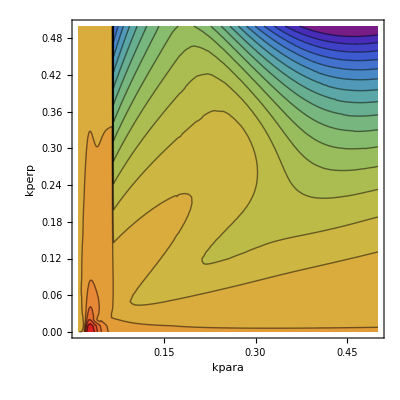

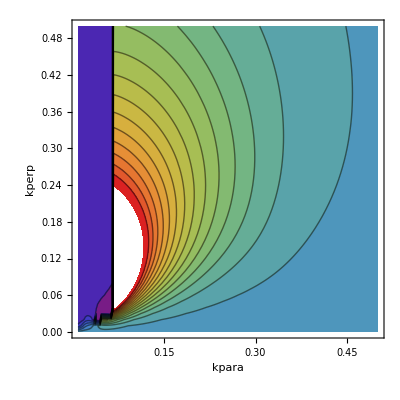

```mathematica
ListContourPlot[Im[freqTotal],DataRange->{{kparamin,kparamax},{kperpmin,kperpmax}},(*关键选项*)AxesLabel->{"kpara","kperp"},Frame->True,ColorFunction->"Rainbow",Contours->20]
ListContourPlot[Re[EyOverExTotal/I*omegaReal/Abs[omegaReal]],DataRange->{{kparamin,kparamax},{kperpmin,kperpmax}},(*关键选项*)AxesLabel->{"kpara","kperp"},Frame->True,ColorFunction->"Rainbow",Contours->20]
```

```mathematica
Export["case1_right2d_gammanew_0.01:0.002:0.5_0:0.02:0.5.csv",Im[freqTotal]];
Export["case1_right2d_RePnew_0.01:0.002:0.5_0:0.02:0.5.csv",Re[EyOverExTotal/I*omegaReal/Abs[omegaReal]]];
```